## d contains (x,y) pairs to train on

```mathematica
d = Table[{x,Sin[2 x]},{x,0,1,0.05}];
```

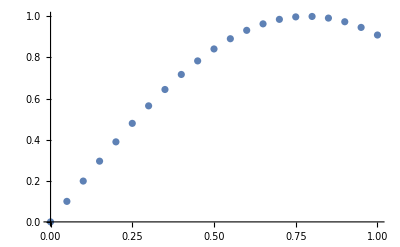

```mathematica
ListPlot[d]
```

## Interrogate trained nn on (x,y) pairs

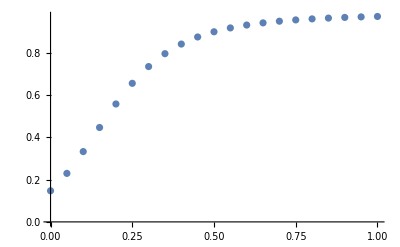

InterpolatingFunction[…]

```mathematica
nnfunc = {{0.0,0.14712323950224485},{0.05,0.2293790595676473},{0.1,0.3324990926023674},{0.15,0.4463934775455663},{0.2,0.5575998467467955},{0.25,0.6552878475991295},{0.3,0.7345128865309876},{0.35,0.7954460333690102},{0.4,0.8409167158020173},{0.45,0.8744047967497044},{0.5,0.8990285699083352},{0.55,0.9172379490641815},{0.6,0.930838849317555},{0.65,0.9411225305691968},{0.7,0.9490011411708084},{0.75,0.9551180520051812},{0.8,0.9599292051450298},{0.85,0.963760426970981},{0.9,0.9668469899196217},{0.95,0.9693607274789401},{1.0,0.9714286280740819}}
ListPlot[nnfunc]
f=Interpolation[nnfunc,InterpolationOrder->3]
Plot[{f[x],2 Cos[2 x]},{x,0,1}]
```

## Find the derivative of the InterpolatingFunction

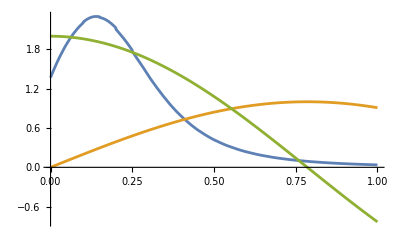

```mathematica
g[x_]=D[f[x],x];
Plot[{g[x],Sin[2 x],2 Cos[2 x]},{x,0,1}]
```

Blue curve looks like derivative coming from NN derivative, green is analytical derivative 2cos(2x)

```mathematica
nnderiv = {{0.0,1.4046167075593057},{0.05,1.876327538707385},{0.1,2.213430475255756},{0.15,2.2951594038522516},{0.2,2.115859756592188},{0.25,1.775588780206755},{0.3,1.394911446020561},{0.35,1.0525313772217764},{0.4,0.7782127687042928},{0.45,0.571788012870739},{0.5,0.42131084147419445},{0.55,0.31303675612243526},{0.6,0.23525708087730407},{0.65,0.1790938404988415},{0.7,0.13816832235088042},{0.75,0.10800912707077955},{0.8,0.0855101533456155},{0.85,0.06851410762508922},{0.9,0.055515118637979984},{0.95,0.04545349349281425},{1.0,0.03757614923551019}};
```

## See how well mma derivative and nn derivative match up

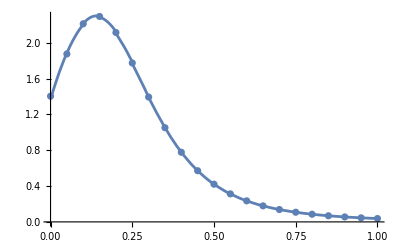

```mathematica
Show[{ListPlot[nnderiv],Plot[g[x],{x,0,1}]}]
```

Match is great